# Saving Face Analysis of the Model Building Routine

## The basic premise of the 3D Model

## Expected Input (Transformed Depth Data such that the Head is placed in the correct orientation in model space)

#### Generis Algorithm for constructing the model While[Frames < N] Read in byte stream Get Fixed Point, and Yaw Pitch and Roll From SDK Calculate Transformation Matix Based On Yaw Pitch and Roll Determine Relative Location Of Head SDK. (No need to process everything) For[Vertices] Apply Linear Transform to bring point relative to origin Apply Rotational Transform To Align Head //Error Checking Make Sure Point is In Model Space Map Point to Model Byte[] Increase that point by one Save Model End

### To Transform a series of 3D vertices into hits on a 3 dimensional byte array

#### The X, Y and Z indices of the Array represent a fixed offset from a predetermined minimum in x,y,z where the point <0,0,0> is x_(min,)Y_(min,) Z_min

#### The point <n,m,k> translates to <X_min + Δ_x*n, Y_min + Δ_y*m, Z_min + Δ_y * k)

### Given Parameters (Temporary values) units are in meters

#### These are adjustable for tunable performance.

```mathematica
xmin = -0.25;
ymin = -0.25;
zmin = -.1;
xmax = 0.25;
ymax = 0.25;
zmax = 0.4;
deltax = 0.0025;
deltay = 0.0025;
deltaz = 0.0025;
xind = (xmax - xmin)/deltax//N;
yind = (ymax - ymin)/deltay//N;
zind = (zmax - zmin)/deltaz//N;
model = Table[0,{i,1, xind * yind * zind}];
lengthx = yind*zind;
lengthy = zind;
```

```mathematica
Length[model]
```

```mathematica
8000000 (*Huge... Probably Need to Dial Down The Deltas*)
```

Function to Transform Coords To Model Space

```mathematica
CoordTransform[vertex_]:={Floor[(vertex[[1]]-xmin)/deltax],Floor[(vertex[[2]]-ymin)/deltay],Floor[(vertex[[3]]-zmin)/deltaz]}
```

Smoke Test Transform Function

```mathematica
CoordTransform[{xmin,ymin,zmin}]
```

{0,0,0}

```mathematica
CoordTransform[{xmax,ymax,zmax}]
```

{200,200,200}

```mathematica
CoordTransform[{0.123567,-0.23363424,-0.23657342}]
```

{149,6,85}

Model Point Increment Function Note(In Mathematica Array index starts at 1)

```mathematica
ApplyCoord[index_]:= Module[{},
model[[(index[[1]]-1)*lengthx + (index[[2]]-1)*lengthy +index[[3]]]]=model[[(index[[1]]-1)*lengthx + (index[[2]]-1)*lengthy +index[[3]]]] + 1;
];
```

Test Should Increment each value in the array exactly once

```mathematica
Dynamic[{i,j,k}]
For[i=1,i≤xind,i++,
For[j=1,j≤yind,j++,
For[k=1,k≤zind,k++,
ApplyCoord[{i,j,k}]
];
];
];
```

Check

```mathematica
DeleteDuplicates[model[[1;;100]]]
```

{1}

## Transform Module

### Move points To Origin

```mathematica
MoveToOrigin[vertex_,referenceVertex_]:= {vertex[[1]] - referenceVertex[[1]],vertex[[2]] - referenceVertex[[2]],vertex[[3]] - referenceVertex[[3]]}
```

### Smoke Test

```mathematica
refV = {100,100,100};
MoveToOrigin[refV,refV](*Should Return {0,0,0}*)
```

{0,0,0}

### Magnitude of the vector

```mathematica
Magnitude[vertex_] :=√(vertex[[1]]^2 +vertex[[2]]^2 + vertex[[3]]^2) //N
```

### Smoke Test

```mathematica
Magnitude[{1,1,1}]
```

Magnitude[{1,1,1}]

### Rotate a point around the origin in x, y, z

#### Basic Equations

```mathematica
RotateX[vertex_,θ_] := vertex  . {{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}}
RotateY[vertex_,θ_] := vertex  . {{Cos[θ],0,Sin[θ]},{0,1,0},{-Sin[θ],Sin[θ],Cos[θ]}}
RotateZ[vertex_,θ_] := vertex  . {{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}
```

#### This Method Calculates The Matrix Once and Reuses the calculations

```mathematica
SetRotationMatrixX[θ_]:= Module[{},Tx = {{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}}//N]; (*Expensive Operation only do once perframe*)
SetRotationMatrixY[θ_]:= Module[{},Ty = {{Cos[θ],0,Sin[θ]},{0,1,0},{-Sin[θ],0,Cos[θ]}}//N]; (*Expensive Operation only do once perframe*)
SetRotationMatrixZ[θ_]:= Module[{},Tz =  {{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}//N]; (*Expensive Operation only do once perframe*)
SetCombinedMatrix[θ_,ϕ_,ρ_]:= Module[{},
SetRotationMatrixX[θ];
SetRotationMatrixY[ϕ];
SetRotationMatrixZ[ρ];
Tm = Tx . Ty  . Tz;
];
```

```mathematica
ApplyTransform[v_]:=v.Tm
```

#### Test Method

```mathematica
TestPoint[v_,test_]:=Module[{},
SetCombinedMatrix[test[[1]],test[[2]],test[[3]]];
Return[v . Tm]
];
```

```mathematica
Manipulate[ListPointPlot3D[Table[TestPoint[{1,1,1},{x,y,0}],{x,0,2π,.01}],PlotRange->{{-2,2},{-2,2},{-2,2}}],{y,0,2π}]
```

```mathematica
ListPointPlot3D[{Table[RotateX[{0,1,0},p],{p,0,2π,.01}],Table[RotateY[{1,0,0},p],{p,0,2π,.01}],Table[RotateZ[{0,1,0},p],{p,0,2π,.01}]}]
```

-Graphics3D-

## Test On Actual Data

### To Validate the assumption that the Point of Origin and Yaw, Pitch and Roll have been gathered. They will be manually Calculated for this Analysis.

```mathematica
FileNameSetter[Dynamic[image1]]
```

File Selected

```mathematica
image1
```

G:\camera_uvmap\test\test_1_5.csv

{{-0.0444447,-0.03565,0.586},{-0.0445167,-0.0331572,0.587},{-0.0471449,-0.035715,0.587},{-0.0523965,-0.0357241,0.587},{-0.0472212,-0.0332176,0.588},{-0.0419684,-0.0357677,0.588},{-0.0472295,-0.0383348,0.588},{-0.0420362,-0.0332665,0.589},{-0.0499444,-0.0384047,0.589},{-0.0446807,-0.0409592,0.589},{-0.052585,-0.0409744,0.589},{-0.0500246,-0.035902,0.59},{-0.0447522,-0.0384607,0.59},{-0.0526691,-0.038475,0.59},{-0.0473948,-0.0410336,0.59},{-0.0448371,-0.0436715,0.591},{-0.0501898,-0.0334477,0.592},{-0.0528383,-0.0334521,0.592},{-0.0422578,-0.0385868,0.592},{-0.0502037,-0.0411777,0.592}}

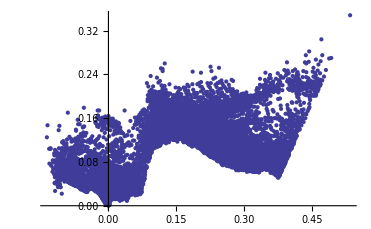
-Graphics3D- | -Graphics-

```mathematica
Image1 = Import[image1];
Image1 = Select[Image1,#[[1]] > -0.25 ∧ #[[1]]< 0.25&];
Image1 = Sort[Image1,#1[[3]] < #2[[3]] &];
Image1[[1;;20]]
v1 = Image1[[1]];
For[k = 1, k ≤Length[Image1],k++,
Image1[[k]] = MoveToOrigin[Image1[[k]],v1];
];
{{ListPointPlot3D[Image1, AspectRatio->1, BoxRatios->{1,1,1}],ListPlot[Image1[[1;;,2;;3]]]}}//TableForm
```

## Test Build Model (Zeroed But Not Oriented) Can be safely Multi-threaded

```mathematica
BuildModel[image_]:=Module[{},
For[k=1, k <= Length[image], k++,
If[image[[k,1]] >= xmin ∧ image[[k,1]] ≤ xmax ∧
image[[k,2]] >= ymin ∧ image[[k,2]] ≤ ymax ∧
image[[k,3]] >= zmin ∧ image[[k,3]] ≤ zmax ,
ApplyCoord[CoordTransform[image[[k]]]];
];
];
];
```

```mathematica
Dynamic[k]
```

```mathematica
BuildModel[Image1]
```

```mathematica
DeleteDuplicates[model]
```

{0,1}

### Test Reverse Engineers the model

```mathematica
modelDat = {};
Dynamic[{x,y,z}]
For[x = 1, x <= xind,x++,
For[y = 1, y <= yind,y++,
For[z = 1, z <= zind,z++,
If[model[[((x - 1) * lengthx) + ((y - 1) * lengthy) + z]]≥1,
modelDat = Append[modelDat, { x,y,z}];
];
];
];
];
```

```mathematica
Length[modelDat]
```

9721

### Static View Of Model

```mathematica
ListPointPlot3D[modelDat, AspectRatio->1,BoxRatios->{1,1,1},PlotRange->All]
```

-Graphics3D-

### Model Rotated 45 Degrees about x and y

```mathematica
SetCombinedMatrix[π/4,π/4,0];
modelDat=Map[ApplyTransform,modelDat];
ListPointPlot3D[modelDat, AspectRatio->1,BoxRatios->{1,1,1},PlotRange->All]
```

-Graphics3D-

```mathematica
TestRotate[x_,y_,z_]:= Module[{},
SetCombinedMatrix[x,y,z];
Return[Map[ApplyTransform,modelDat]]
];
```

### Model Rotated in any direction

```mathematica
Manipulate[ListPointPlot3D[TestRotate[x,y,z],AspectRatio->1,BoxRatios->{1,1,1},PlotRange->All],{x,0,2π},{y,0,2π},{z,0,2π}]
```